```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Marchevsky\integrator\addons

```mathematica
R=1;
n=16;
```

```mathematica
pts=Table[{i,R Cos[(2π)/n(i-1)],R Sin[(2π)/n(i-1)],0},{i,n}]//N;
```

```mathematica
topo=Table[{i,102,i,i+1},{i,n-1}]~Join~{{n,102,n,1}};
```

```mathematica
toFile={{n,n}}~Join~pts~Join~topo;
```

```mathematica
Export["G2-16.dat",toFile,"Table"];
```

```mathematica
ri=(pts[[1,2;;3]]+pts[[2,2;;3]])/2
```

{0.96194,0.191342}

```mathematica
pnlA=pts[[2,2;;3]]
pnlB=pts[[3,2;;3]]
```

{0.92388,0.382683}

{0.707107,0.707107}

```mathematica
NIntegrate[1/(2π)Log[1/Norm[ri-{x,y}]],{x,y}∈Line[{pnlA,pnlB}]]
```

0.0622921

```mathematica
0.028126500157064145
```

0.0281265

```mathematica
0.028126500157060856-0.028126500157064145
```

-3.28904×10^-15

```mathematica
resA={{100,1.394/100^2},{200,5.572/100^2},{400,20.94/100^2},{800,7.277/1000},{1600,14.67/500}}
```

{{100,0.0001394},{200,0.0005572},{400,0.002094},{800,0.007277},{1600,0.02934}}

```mathematica
resA={{100,0.0703/500},{200,0.2727/500},{400,1.103/500},{800,4.407/500},{1600,14.67/500}}
```

{{100,0.0001406},{200,0.0005454},{400,0.002206},{800,0.008814},{1600,0.02934}}

```mathematica
resA[[2;;,2]]/resA[[;;-2,2]]
```

{3.87909,4.04474,3.99547,3.3288}

```mathematica
cnt=1/2(pts[[;;,{2,3}]]+RotateLeft[pts[[;;,{2,3}]]]);
```

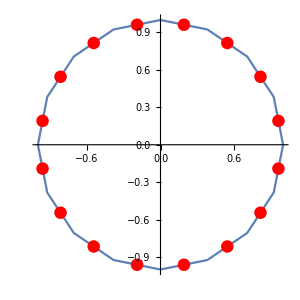

```mathematica
figCirc=Show[ListLinePlot[pts[[;;,{2,3}]]~Join~{pts[[1,{2,3}]]},AspectRatio->Automatic],ListPlot[1/2(pts[[;;,{2,3}]]+RotateLeft[pts[[;;,{2,3}]]]),PlotStyle->Directive[Red,PointSize[0.03]]],AxesStyle->Directive@{Black,16,FontFamily->"Times"},ImageSize->300]
```

```mathematica
Export["figCirc.pdf",figCirc]
```

figCirc.pdf

```mathematica
result=Flatten@Table[NIntegrate[1/(2π)Log[1/Norm[cnt[[i]]-{x,y}]],{x,y}∈Line[{pts[[j,2;;3]],pts[[If[j<n,j+1,1],2;;3]]}]],{i,n},{j,n}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.499984}. NIntegrate obtained 0.163587 and 4.3239×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.499984}. NIntegrate obtained 0.163587 and 4.3239×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.499984}. NIntegrate obtained 0.163587 and 4.3239×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
CppResult=Import["result.txt","Table"]//Flatten;
```

```mathematica
MinMax[result-CppResult]
```

{-7.70133×10^-7,2.498×10^-16}

```mathematica
result=Partition[Flatten@Table[If[i==j,{0,0},NIntegrate[1/(2π)(cnt[[i]]-{x,y})/((cnt[[i]]-{x,y}).(cnt[[i]]-{x,y})),{x,y}∈Line[{pts[[j,2;;3]],pts[[If[j<n,j+1,1],2;;3]]}]]],{i,n},{j,n}],2];
```

```mathematica
CppResult=Partition[Flatten@Import["result.txt","Table"],2];
```

```mathematica
MinMax[Norm[#]&/@(result-CppResult)]
```

{0,1.74913×10^-12}

```mathematica
result=Partition[Flatten@Table[If[i==j,{0,0},NIntegrate[1/(2π)({xx,yy}-{x,y})/(({xx,yy}-{x,y}).({xx,yy}-{x,y})),{xx,yy}∈Line[{pts[[i,2;;3]],pts[[If[i<n,i+1,1],2;;3]]}],{x,y}∈Line[{pts[[j,2;;3]],pts[[If[j<n,j+1,1],2;;3]]}]]],{i,n},{j,n}],2];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.78991×10^-20 and 2.2169×10^-19 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.17582×10^-20 and 2.23234×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.91641×10^-20 and 2.62901×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
CppResult=Partition[Flatten@Import["result.txt","Table"],2];
```

```mathematica
MinMax[Norm[#]&/@(result-CppResult)]
```

{0,1.59594×10^-9}

```mathematica
result=Flatten@Table[NIntegrate[1/(4π)Log[1/(({xx,yy}-{x,y}).({xx,yy}-{x,y}))],{xx,yy}∈Line[{pts[[i,2;;3]],pts[[If[i<n,i+1,1],2;;3]]}],{x,y}∈Line[{pts[[j,2;;3]],pts[[If[j<n,j+1,1],2;;3]]}]],{i,n},{j,n}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0591497 and 0.0000103142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0591497 and 0.0000103142 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0591497 and 0.0000103142 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
CppResult=Flatten@Import["result.txt","Table"];
```

```mathematica
MinMax[result-CppResult]
```

{2.82941×10^-12,1.01502×10^-6}

```mathematica
result-CppResult
```

{1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24177×10^-11,2.26478×10^-10,5.31301×10^-11,1.52836×10^-11,5.06809×10^-12,2.82941×10^-12,5.06813×10^-12,1.52835×10^-11,5.31302×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24177×10^-11,2.26478×10^-10,5.313×10^-11,1.52836×10^-11,5.06813×10^-12,2.82941×10^-12,5.06811×10^-12,1.52835×10^-11,5.31301×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24176×10^-11,2.26478×10^-10,5.31301×10^-11,1.52835×10^-11,5.06811×10^-12,2.82941×10^-12,5.06813×10^-12,1.52836×10^-11,5.313×10^-11,2.26478×10^-10,4.24177×10^-11,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24177×10^-11,2.26478×10^-10,5.31302×10^-11,1.52835×10^-11,5.06813×10^-12,2.82941×10^-12,5.06809×10^-12,1.52836×10^-11,5.31301×10^-11,2.26478×10^-10,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24177×10^-11,2.26478×10^-10,5.31301×10^-11,1.52836×10^-11,5.06809×10^-12,2.82941×10^-12,5.06813×10^-12,1.52835×10^-11,5.31302×10^-11,5.31301×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24177×10^-11,2.26478×10^-10,5.313×10^-11,1.52836×10^-11,5.06813×10^-12,2.82941×10^-12,5.06811×10^-12,1.52835×10^-11,1.52836×10^-11,5.313×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24176×10^-11,2.26478×10^-10,5.31301×10^-11,1.52835×10^-11,5.06811×10^-12,2.82941×10^-12,5.06813×10^-12,5.06809×10^-12,1.52836×10^-11,5.31301×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24177×10^-11,2.26478×10^-10,5.31302×10^-11,1.52835×10^-11,5.06813×10^-12,2.82941×10^-12,2.82941×10^-12,5.06813×10^-12,1.52835×10^-11,5.31302×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24177×10^-11,2.26478×10^-10,5.31301×10^-11,1.52836×10^-11,5.06809×10^-12,5.06813×10^-12,2.82941×10^-12,5.06811×10^-12,1.52835×10^-11,5.31301×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24177×10^-11,2.26478×10^-10,5.313×10^-11,1.52836×10^-11,1.52835×10^-11,5.06811×10^-12,2.82941×10^-12,5.06813×10^-12,1.52836×10^-11,5.313×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24176×10^-11,2.26478×10^-10,5.31301×10^-11,5.31302×10^-11,1.52835×10^-11,5.06813×10^-12,2.82941×10^-12,5.06809×10^-12,1.52836×10^-11,5.31301×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24177×10^-11,2.26478×10^-10,2.26478×10^-10,5.31301×10^-11,1.52836×10^-11,5.06809×10^-12,2.82941×10^-12,5.06813×10^-12,1.52835×10^-11,5.31302×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,4.24177×10^-11,4.24177×10^-11,2.26478×10^-10,5.313×10^-11,1.52836×10^-11,5.06813×10^-12,2.82941×10^-12,5.06811×10^-12,1.52835×10^-11,5.31301×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,2.58318×10^-11,2.58318×10^-11,4.24176×10^-11,2.26478×10^-10,5.31301×10^-11,1.52835×10^-11,5.06811×10^-12,2.82941×10^-12,5.06813×10^-12,1.52836×10^-11,5.313×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6,8.93969×10^-11,8.93969×10^-11,2.58318×10^-11,4.24177×10^-11,2.26478×10^-10,5.31302×10^-11,1.52835×10^-11,5.06813×10^-12,2.82941×10^-12,5.06809×10^-12,1.52836×10^-11,5.31301×10^-11,2.26478×10^-10,4.24177×10^-11,2.58318×10^-11,8.93969×10^-11,1.01502×10^-6}